# MA2330

## Chapter 3 : Determinants

### 3.1 Intro

Starting slow we want to understand where the scalar
	a d - b c
comes from in the expression 
	(a | b
c | d)^-1=1/(a d-b c)(d | -b
-c | a)
It turns up if we just multiply

```mathematica
MatrixForm[({{a, b}, {c, d}}).({{d, -b}, {-c, a}})]
```

(-b c+a d | 0
0 | -b c+a d)

This determinant was useful because the matrix (a | b
c | d) was invertible iff a d- b c≠0. 
For a three by three we can row reduce and get

```mathematica
A=Table[Subscript[a, i,j],{i,3},{j,3}];REF=A;
MatrixForm[REF]
REF=RowScale[REF,{2,Subscript[a, 1,1]}];
REF=RowScale[REF,{3,Subscript[a, 1,1]}];
REF=RowAdd[REF,{
{{2,-Subscript[a, 2,1]},{3,-Subscript[a, 3,1]}},
1}];
```

(a_(1,1) | a_(1,2) | a_(1,3)
a_(2,1) | a_(2,2) | a_(2,3)
a_(3,1) | a_(3,2) | a_(3,3))

(a_(1,1) | a_(1,2) | a_(1,3)
a_(1,1) a_(2,1) | a_(1,1) a_(2,2) | a_(1,1) a_(2,3)
a_(3,1) | a_(3,2) | a_(3,3))row_(RowBox[{)
row_(RowBox[{)→(a_(1,1))row_(RowBox[{)
row_(RowBox[{)

(a_(1,1) | a_(1,2) | a_(1,3)
a_(1,1) a_(2,1) | a_(1,1) a_(2,2) | a_(1,1) a_(2,3)
a_(1,1) a_(3,1) | a_(1,1) a_(3,2) | a_(1,1) a_(3,3))row_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)→(a_(1,1))row_(RowBox[{)

(a_(1,1) | a_(1,2) | a_(1,3)
0 | -a_(1,2) a_(2,1)+a_(1,1) a_(2,2) | -a_(1,3) a_(2,1)+a_(1,1) a_(2,3)
0 | -a_(1,2) a_(3,1)+a_(1,1) a_(3,2) | -a_(1,3) a_(3,1)+a_(1,1) a_(3,3))row_(RowBox[{)
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_,)
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_,)

We can continue row reducing if our next pivot (in the 2,2 slot) 
	-a_(1,2) a_(2,1)+a_(1,1) a_(2,2) ≠0

```mathematica
REF=RowScale[REF,{3, REF⟦2,2⟧}];
REF=RowAdd[REF,{{{3, -(-Subscript[a, 1,2] Subscript[a, 3,1]+Subscript[a, 1,1] Subscript[a, 3,2])}},2}];
REF⟦3,3⟧
```

(a_(1,1) | a_(1,2) | a_(1,3)
0 | -a_(1,2) a_(2,1)+a_(1,1) a_(2,2) | -a_(1,3) a_(2,1)+a_(1,1) a_(2,3)
0 | (-a_(1,2) a_(2,1)+a_(1,1) a_(2,2)) (-a_(1,2) a_(3,1)+a_(1,1) a_(3,2)) | (-a_(1,2) a_(2,1)+a_(1,1) a_(2,2)) (-a_(1,3) a_(3,1)+a_(1,1) a_(3,3)))row_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)→(-a_(1,2) a_(2,1)+a_(1,1) a_(2,2))row_(RowBox[{)

(a_(1,1) | a_(1,2) | a_(1,3)
0 | -a_(1,2) a_(2,1)+a_(1,1) a_(2,2) | -a_(1,3) a_(2,1)+a_(1,1) a_(2,3)
0 | 0 | a_(1,1) (a_(1,3) (-a_(2,2) a_(3,1)+a_(2,1) a_(3,2))+a_(1,2) (a_(2,3) a_(3,1)-a_(2,1) a_(3,3))+a_(1,1) (-a_(2,3) a_(3,2)+a_(2,2) a_(3,3))))row_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{RowBox[{SubscriptBox[)_,)

a_(1,1) (a_(1,3) (-a_(2,2) a_(3,1)+a_(2,1) a_(3,2))+a_(1,2) (a_(2,3) a_(3,1)-a_(2,1) a_(3,3))+a_(1,1) (-a_(2,3) a_(3,2)+a_(2,2) a_(3,3)))

This is a_11 times the determinant of the 3×3 matrix. We need to look at this carefully to see how to compute it.  We also need to work out how to define and compute a determinant for 4×4 matrices and larger.

a_(1,1) (a_(1,3) (-a_(2,2) a_(3,1)+a_(2,1) a_(3,2))+a_(1,2) (a_(2,3) a_(3,1)-a_(2,1) a_(3,3))+a_(1,1) (-a_(2,3) a_(3,2)+a_(2,2) a_(3,3)))

Definition: For n>=2 the determinant of A∈ℝ^(n×n) is the sum
	det(A)=∑_(j=1)^n (-1)^(1+j)a_(1,j) det(𝔸_(1,j))
where the (n-1)×(n-1) matrices 𝔸_(i,j) are simply the matrix A with the i^th row and j^th column deleted.  The term C_(i,j)=(-1)^(i+j)det(𝔸_(i,j)) is called the (i,j)-cofactor C_(i,j)=(-1)^(i+j) det(A_(i,j)) of A.

Theorem 1: There is nothing special about the first row. You can compute the determinant using the cofactor expansion about the i^th row 
	det(A)=∑_(j=1)^n (-1)^(i+j)a_(i,j) det(𝔸_(i,j))=∑_(j=1)^n a_(i,j) C_(i,j)=a_(i,1)C_(i,1)+…+ a_(i,n)C_(i,n)
or the j^th column
	det(A)=∑_(i=1)^n (-1)^(i+j)a_(i,j) det(𝔸_(i,j))=a_(1,j)C_(1,j)+…+ a_(n,j)C_(n,j)

The (-1)^(i+j) in the definition of the cofactor is a simple checker board pattern.

```mathematica
n=4;
TabView[{
"values"->MatrixForm[Table[(-1)^(i+j),{i,1, n},{j,1,n}]],
"pic"->MatrixPlot[Table[(-1)^(i+j),{i,1, n},{j,1,n}]]
},2]
```

If asked to compute a determinant you should pick a convenient column or row!  All rows are convenient for a triangular matrix.

Theorem 2: If T is a triangular n×n matrix then det(T) is the product of the diagonal entries
	det(T)=T_(1,1)×T_(2,2)×…×T_(n,n)=Π_(i=1)^n T_(i,i)

A general co-factor expansion is incredibly slow for a large n×n matrix A. The cofactor expression reduces the computation of det(A) to the sum of n smaller - (n-1)×(n-1) - matrices.  If W(n) is a measure of how much work it is to compute the determinant using the cofactor expansion then
	w(n)≈n×w(n-1)+n multiplications and additions.
Ignoring the extra multiplications and additions we have
	w(n)=n w(n-1) 
which has the solution w(n)=c n!.  If A∈ ℝ^(n×n)and n=30 then computing det(A) using the co-factor expansion is w(30)=c 30! = c 265252859812191058636308480000000. This is not practical.  In an algorithm class this is called an algorithm with an exponential growth rate.

The next section 3.2 gives us a practical algorithm with complexity  c n^3.  It is just row-reduction.

```mathematica
30!
```

265252859812191058636308480000000

### 3.2 Properties

Row operations change the determinant of a matrix in simple ways!

Theorem 3: Row Operations on a square matrix A.
a) det(B)=det(A) if B is obtained from A by adding a multiple of one row to another. 
b) det(B)=-det(A) if B is obtained from A by switching two rows. 
b) det(B)=k det(A) if B is obtained from A by scaling one row by k.

```mathematica
A=REF={{1,-4,2},{-2,8,-9},{-1,7,0}};
MatrixForm[REF]
REF=RowAdd[REF,{{{2,2},{3,1}},1}];
REF=RowSwitch[REF,{2,3}];
```

(1 | -4 | 2
-2 | 8 | -9
-1 | 7 | 0)

(1 | -4 | 2
0 | 0 | -5
0 | 3 | 2)row_(RowBox[{)
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))

(1 | -4 | 2
0 | 3 | 2
0 | 0 | -5)row_(RowBox[{)
row_(RowBox[{)→row_(RowBox[{)
row_(RowBox[{)→row_(RowBox[{)

Computers compute the determinant of a square n×n matrix A by row reducing to to an echelon form U and then multiplying the diagonal elements together.  In symbols,
	det(A) = ±det(U) = (-1)^r u_11×u_22×…×u_nn=(-1)^r Π_(i=1)^n u_ii 
The matrix A is invertible iff it has a pivot entry in each row.  The matrix A is invertible iff det(A)≠0.

The complexity of reducing A to echelon form U is w(n)=c n^3.

To reduce the first column you need to compute the (n-1)×(n-1) block below and to the left of the 1,1 entry: this is (n-1)^2 multiplications and additions.

To reduce the second column you need to compute the (n-2)×(n-2) block below and to the left of the 2,2 entry: this is (n-2)^2 multiplications and additions.

To reduce the third column column you need to compute the (n-3)×(n-3) block below and to the left of the 3,3 entry: this is (n-3)^2 multiplications and additions.

…

Adding up these operations gives ∑_(i=1)^n (n-i)^2=1/6 (n-3 n^2+2 n^3)≈2/6 n^3≈c n^3

An n^3 algorithm is practical and exponential algorithm is not!

```mathematica
n=25;
{1/6 (n-3 n^2+2 n^3),0.333 n^3 ,n!}
```

{4900,5203.13,15511210043330985984000000}

Theorem 6. Multiplicative Property
If A and B are n×n matrices then det(A B)=det(A)det(B)

Warning:   det(A +B)≠det(A)+det(B)

However, changing one column of a matrix does give a linear transformation!

```mathematica
n=4;
A=RandomInteger[{-9,9},{n,n}];
j=2;
{u,v}=RandomReal[{-1,1},{2,n}];
ANew=A;ANew⟦All,j⟧=u;
TabView[Map[MatrixForm,{A,ANew}]]
```

12

```mathematica
T[x_,j_,A_]:= Module[{ANew=A}, 
ANew⟦All,j⟧=x;
Det[ANew]]
{u,v}=RandomReal[{-1,1},{2,n}];
{T[u,j,A]+T[v,j,A],T[u+v,j,A]}
```

{-222.557,-222.557}

Remember computing determinants using row-reduction is just as much work as solving a linear system. Computing determinants using the cofactor expansion is impossible for non-tiny matrices.  The next section is of theoretical interest only.

### 3.2 Cramer’s Rule and Volume

#### Cramer’s Rule

Cramer’s rule is a formula for the components of the solution of A x=b which uses determinants.

Theorem 7: Cramer’s Rule
The coordinates of the solution of A x =b are 
	x_i=det(A_i(b))/det(A)
where A_i(b) is the matrix A with the i^th column replaced by the vector b.

The proof of this is cute!  This is probably why it is in all the linear algebra texts! 
	A Id_i(x)=A (e_1… e_(i-1)x e_(i+1)… e_n)=(Ae_1… Ae_(i-1)x Ae_(i+1)… Ae_n)=(a_1… a_(i-1)b a_(i+1)… a_n)=A_i(b)
so
	det(A)det(I_i(x))=det(A)x_i det(A_i(b)) .

#### Inverses

The solution of A x=e_j is just the j^th column of A^-1 so
	(A^-1)_(i,j)=(det(A_i(e_j)))/(det(A)).
The determinant on the top is actually something we have seen before. A direct computation shows that 
	det(A_i(e_j))=(-1)^(i+j)det A_(j,i)=C_(j,i)
are the cofactors we computed earlier by removing row j and column i from the matrix A. With this notation
	A^-1=1/(det(A))(C_(1,1) | C_(2,1) | ⋯ | C_(n,1)
C_(1,2) | C_(2,2) | ⋯ | C_(n,2)
⋮ | ⋮ |   | ⋮
C_(1,2) | C_(2,n) | ⋯ | C_(n,2))=1/(det(A))adj(A)
The matrix of cofactors is the adjugate of A

#### Volumes etc.

The absolute value of the determinant of a 2×2 matrix (a_1 | a_2) is the area of the parallelogram with sides a_1 and a_2.

```mathematica
Parallelogram
```

Parallelogram

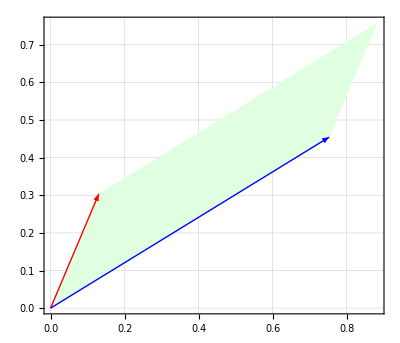

```mathematica
A=RandomReal[{0,1},{2,2}];
{a1,a2}={A⟦All,1⟧,A⟦All,2⟧};
Graphics[{
{LightGreen,Parallelogram[{0,0},{a1,a2}]},
{Red, Arrow[{{0,0},a1}]},
{Blue, Arrow[{{0,0},a2}]}
},
AspectRatio->Automatic,Frame->True,GridLines->Automatic]
```

The absolute value of the determinant of a 3×3 matrix (a_1 | a_2 | a_3) is the volume of the parallelepiped with sides a_1 and a_2 and a_3.

```mathematica
A=RandomReal[{0,1},{3,3}];
{a1,a2,a3}={A⟦All,1⟧,A⟦All,2⟧,A⟦All,3⟧};
Graphics3D[{Thickness[0.015],
{LightGreen,Parallelepiped[{0,0,0},{a1,a2,a3}]},
{Red, Arrow[{{0,0,0},a1}]},
{Blue, Arrow[{{0,0,0},a2}]},
{Orange, Arrow[{{0,0,0},a3}]}
},
BoxRatios->Automatic,Boxed->True,FaceGrids->All,Axes->True]
```

-Graphics3D-

Our aim is to see why these statements are true! This works because the

```mathematica
A=RandomReal[{0.5,1},{2,2}];
{a1,a2}={A⟦All,1⟧,A⟦All,2⟧};
Animate[
Graphics[{
{LightGreen,Parallelogram[{0,0},{a1,a2}]},
{Purple,Parallelogram[{0,0},{a1,a2+h a1}]}
}],
{h,-1,1}]
```

## Row Op Code

```mathematica
Clear[RowScale,RowSwitch,RowAdd]
RowScale[A_,{i_, α_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
ANew⟦i,All⟧=α ANew⟦i,All⟧;
s⟦i⟧=StringForm["row_(``)→(``)row_(``)",i,α,i];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowSwitch[A_,{i_,j_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→row_(``)",i,j];
s⟦j⟧=StringForm["row_(``)→row_(``)",j,i];
ANew⟦{i,j},All⟧=ANew⟦{j,i},All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowAdd[A_,{i_,α_,p_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
Clear[RowAdd]
RowAdd[A_,{iαs_,p_}]:=Module[{ANew=A,s,i,α},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
Do[
{i,α}=iαs⟦j⟧;
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧,
{j,Length[iαs]}];
ANew=Simplify[ANew];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
```